Start vertex: 1 End vertex: 1259

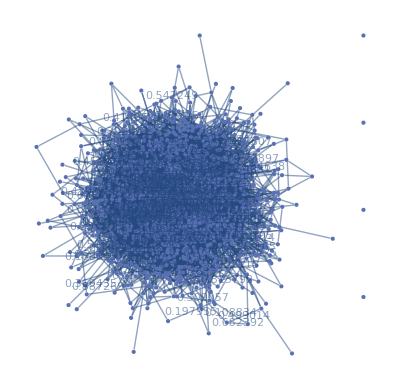
-Graphics-Shortest Path

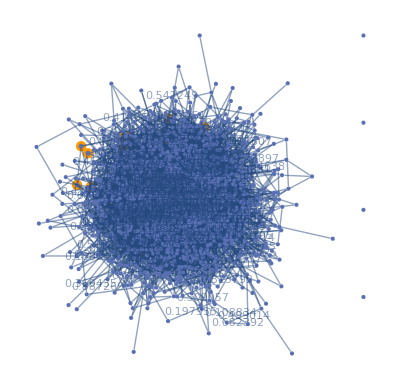
-Graphics-Max Flow = 3

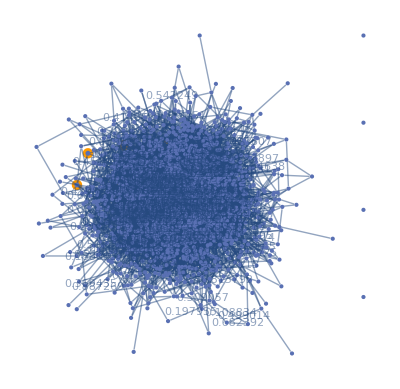
-Graphics-Min Flow = 0

Start vertex: 1 End vertex: 67

Start vertex: 1 End vertex: 6

Start vertex: 1 End vertex: 2

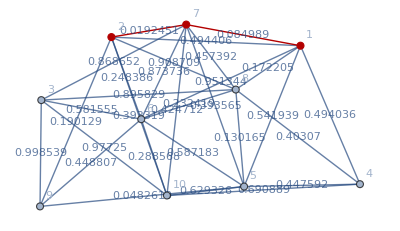

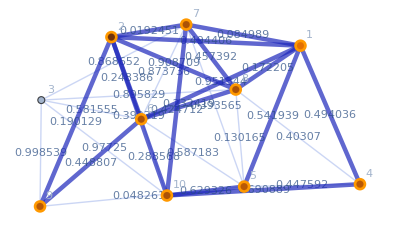

Max Flow = 6

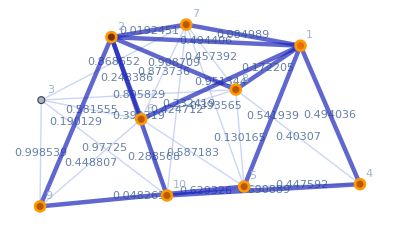

Min Flow = 0

```mathematica
numVertices = 1500; 
numEdges = 3 *numVertices;
g1 = RandomGraph[{numVertices,numEdges},EdgeWeight->RandomReal[{0,1},numEdges],EdgeLabels->"EdgeWeight",VertexLabels->"Name",DirectedEdges->False];
startVertex =1;
endVertex = RandomInteger[{1, numVertices}];
While[startVertex==endVertex, endVertex = RandomInteger[{1, numVertices}]];
str1 =StringForm["Start vertex: `` End vertex: ``",startVertex,endVertex];
Print[str1]
pg = FindShortestPath[g1,startVertex, endVertex];
ℱx  = FindMaximumFlow[g1,startVertex, endVertex,"OptimumFlowData"];
ℱm = FindMinimumCostFlow[g1,startVertex, endVertex,"OptimumFlowData"];
maxFlow = ℱx["FlowValue"];
minFlow =ℱm["FlowValue"];
Labeled[Framed[HighlightGraph[g1, PathGraph[pg]]],"Shortest Path"]
Labeled[Framed[ℱx["FlowGraph"]],
StringForm["Max Flow = ``",maxFlow]]
Labeled[Framed[ℱm["FlowGraph"]],
StringForm["Min Flow = ``",minFlow]]
```